## Figure 3

```mathematica
Clear[Id,RY,θ]
Id=IdentityMatrix[2];
RY[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

RY[θ1].{1,0}
KroneckerProduct[RY[θ1],Id].Flatten[KroneckerProduct[{1,0},{1,0}]]

KroneckerProduct[RY[θ1],RY[θ2]].Flatten[KroneckerProduct[{1,0},{1,0}]]
```

{Cos[θ1/2],Sin[θ1/2]}

{Cos[θ1/2],0,Sin[θ1/2],0}

{Cos[θ1/2] Cos[θ2/2],Cos[θ1/2] Sin[θ2/2],Cos[θ2/2] Sin[θ1/2],Sin[θ1/2] Sin[θ2/2]}

## Figure 4

{Cos[θ1/2] Cos[θ2/2],Cos[θ1/2] Sin[θ2/2],Cos[θ2/2] Sin[θ1/2],Sin[θ1/2] Sin[θ2/2]}

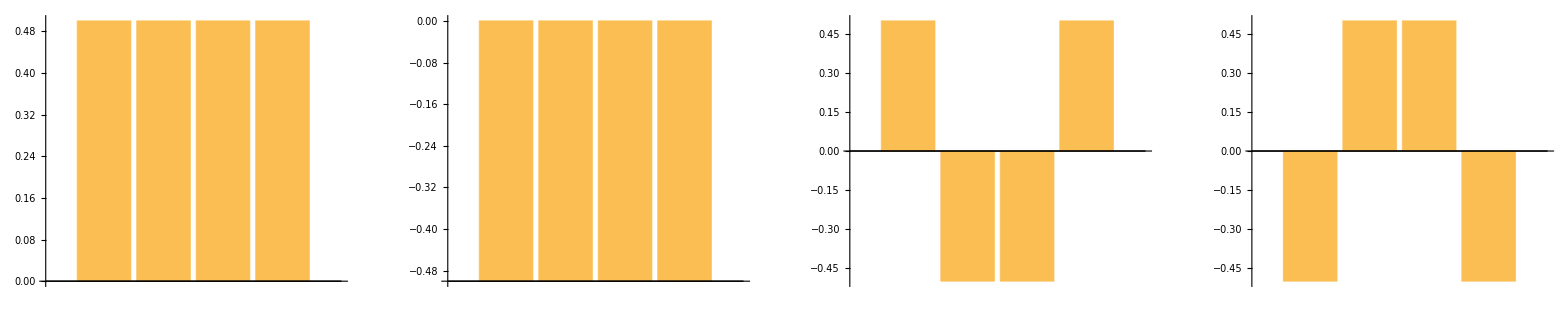

```mathematica
Clear[Id,RY,θ,res]
Id=IdentityMatrix[2];
RY[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

res=KroneckerProduct[RY[θ1],RY[θ2]].Flatten[KroneckerProduct[{1,0},{1,0}]]
GraphicsRow[{BarChart[res/.{θ1->π/2,θ2->π/2},ImageSize->Small],BarChart[res/.{θ1->π/2,θ2->5π/2},ImageSize->Small],BarChart[res/.{θ1->3π/2,θ2->3π/2},ImageSize->Small],BarChart[res/.{θ1->-π/2,θ2->3π/2},ImageSize->Small]},Spacings->20]
```

## Figure 5

{Cos[θ1/2] Cos[θ2/2],Cos[θ1/2] Sin[θ2/2],Cos[θ2/2] Sin[θ1/2],Sin[θ1/2] Sin[θ2/2]}

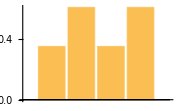

{Cos[θ1/2] Cos[θ2/2],Cos[θ1/2] Sin[θ2/2],Sin[θ1/2] Sin[θ2/2],Cos[θ2/2] Sin[θ1/2]}

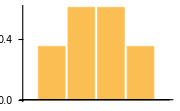

```mathematica
Clear[Id,RY,θ,res,CNOT]
Id=IdentityMatrix[2];
RY[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

CNOT=IdentityMatrix[4];
u=CNOT[[3,;;]];CNOT[[3,;;]]=CNOT[[4,;;]];CNOT[[4,;;]]=u;
CNOT//MatrixForm;

res=KroneckerProduct[RY[θ1],RY[θ2]].Flatten[KroneckerProduct[{1,0},{1,0}]]
BarChart[res/.{θ1->π/2,θ2->2π/3},ImageSize->Small]

res=CNOT.KroneckerProduct[RY[θ1],RY[θ2]].Flatten[KroneckerProduct[{1,0},{1,0}]]
BarChart[res/.{θ1->π/2,θ2->2π/3},ImageSize->Small]
```

## Figure 6

```mathematica
(* import package to facilitate operations on >2 qubits *)
Needs["Quantum`Computing`"];
```

```mathematica
MatrixToDirac[{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}},{2}]
```

Cos[θ/2] |0_OverHat[1]⟩·⟨0_OverHat[1]|+Sin[θ/2] |1_OverHat[1]⟩·⟨0_OverHat[1]|-Sin[θ/2] |0_OverHat[1]⟩·⟨1_OverHat[1]|+Cos[θ/2] |1_OverHat[1]⟩·⟨1_OverHat[1]|

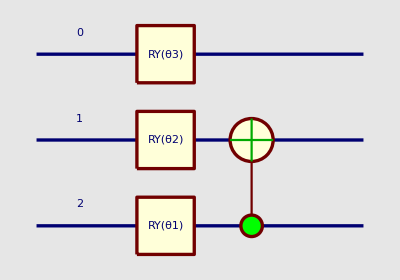

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi,θ1,θ2,θ3,circ,circ1,circ2]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* define RY rotation *)
SetQuantumGate[RY,1,
Function[{q1},
Function[{θ},
Cos[θ/2] |Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+Sin[θ/2] |Subscript[1, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|-Sin[θ/2] |Subscript[0, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| +Cos[θ/2] |Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[RY, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[RY, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ1=(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[1]]]·Subscript[RY, OverHat[0]][θ3]·Subscript[RY, OverHat[1]][θ2]·Subscript[RY, OverHat[2]][θ1];
QuantumPlot[circ1]
U1=QuantumMatrix[circ1];

(* build circuit *)
circ2=(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[0]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[1]]]·Subscript[RY, OverHat[0]][θ3]·Subscript[RY, OverHat[1]][θ2]·Subscript[RY, OverHat[2]][θ1];
QuantumPlot[circ2]
U2=QuantumMatrix[circ2];
```

```mathematica
BarChart[(U1.{1,0,0,0,0,0,0})/.{θ1->π/2,θ2->2π/3,θ3->100/180 π},ImageSize->Small]
BarChart[(U2.{1,0,0,0,0,0,0})/.{θ1->π/2,θ2->2π/3,θ3->100/180 π},ImageSize->Small]
```